```mathematica
sphereTangencyCondition[{x1_,y1_,z1_,r1_}]:= (x-x1)^2+(y-y1)^2+(z-z1)^2==(r1+r)^2;
pane1 =x == r;
pane2 =y  == r;
pane3 =z == r;
bigS = sphereTangencyCondition[{1,1,1,1}]
```

(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2

```mathematica
Table[slst =NSolve[{i[[1]],i[[2]],i[[3]],i[[4]]}];
slst = slst[[Position[r/.slst,Min[r/.slst]][[1]][[1]]]];{sphereTangencyCondition[{x,y,z,r}/.slst],i},{i,{{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,x==r,y==r,z==r},{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,2-x==r,y==r,z==r},{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,2-x==r,2-y==r,z==r},{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,x==r,y==r,2-z==r},{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,x==r,y==r,2-z==r},{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,2-x==r,y==r,2-z==r},{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,2-x==r,2-y==r,2-z==r},{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,x==r,2-y==r,2-z==r}}}]
```

{{(-0.267949+x)^2+(-0.267949+y)^2+(-0.267949+z)^2==(0.267949+r)^2,{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,x==r,y==r,z==r}},{(-1.73205+x)^2+(-0.267949+y)^2+(-0.267949+z)^2==(0.267949+r)^2,{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,2-x==r,y==r,z==r}},{(-1.73205+x)^2+(-1.73205+y)^2+(-0.267949+z)^2==(0.267949+r)^2,{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,2-x==r,2-y==r,z==r}},{(-0.267949+x)^2+(-0.267949+y)^2+(-1.73205+z)^2==(0.267949+r)^2,{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,x==r,y==r,2-z==r}},{(-0.267949+x)^2+(-0.267949+y)^2+(-1.73205+z)^2==(0.267949+r)^2,{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,x==r,y==r,2-z==r}},{(-1.73205+x)^2+(-0.267949+y)^2+(-1.73205+z)^2==(0.267949+r)^2,{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,2-x==r,y==r,2-z==r}},{(-1.73205+x)^2+(-1.73205+y)^2+(-1.73205+z)^2==(0.267949+r)^2,{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,2-x==r,2-y==r,2-z==r}},{(-0.267949+x)^2+(-1.73205+y)^2+(-1.73205+z)^2==(0.267949+r)^2,{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,x==r,2-y==r,2-z==r}}}

```mathematica
nextgen[lst_]:=Module[{slst,xx,yy,zz,rr,xxx,yyy,zzz,rrr,ieq, int,eq5,eq6,gg,ret,works,slst2,x2,y2,z2,r2,thesph},
Return[
Flatten[
Table[
Table[
ieq=sphereTangencyCondition[i[[1]]];
(*Print[j];*);
(*Print[ieq];*);
slst = NSolve[{j[[1]],j[[2]],j[[3]],ieq},{x,y,z,r}];
slst = slst[[Position[r/.slst,Min[Abs[r]/.slst]][[1]][[1]]]];
{xx,yy,zz,rr}={x,y,z,r}/.slst;
int=False;
If[xx-rr<0-10^-9,int=True;eq6=x==r,
If[xx+rr>2+10^-9,int=True;eq6=x==2-r,
If[yy-rr<0-10^-9,int=True;eq6=y==r,
If[yy+rr>2+10^-9,int=True;eq6=y==2-r,
If[zz-rr<0-10^-9,int=True;eq6=z==r,
If[zz+rr>2+10^-9,int=True;eq6=z==2-r,
];
];
];
];
];
];
If[!int,
Do[If[{xxx,yyy,zzz,rrr}=m[[1]];
(EuclideanDistance[{xxx,yyy,zzz},{xx,yy,zz}]<Abs[rrr]+Abs[rr]-1*10^-9),
int=True;
eq6=sphereTangencyCondition[m[[1]]];
Break[];],{m,gglist}];];

If[int,
eq5 = sphereTangencyCondition[{xx,yy,zz,rr}];
gg=False;
Do[
slst2 = NSolve[eeee,{x,y,z,r}];
(*Print[i];
Print["hi4"];*);
slst2 = slst2[[Position[r/.slst2,Min[Abs[r]/.slst2]][[1]][[1]]]];
(*Print["hi3"];*);
{x2,y2,z2,r2}={x,y,z,r}/.slst2;
works=True;
If[x2-r2<0-10^-9||x2+r2>2+10^-9||y2-r2<0-10^-9||y2+r2>2+10^-9||z2-r2<0-10^-9||z2+r2>2+10^-9,works=False];
If[works,
Do[
If[{xxx,yyy,zzz,rrr}=k[[1]];EuclideanDistance[{xxx,yyy,zzz},{x2,y2,z2}]<Abs[rrr]+Abs[r2]-1*10^-6,works=False;Break[];],{k,gglist}];];
If[works,thesph={{x2,y2,z2,r2},eeee};gg=True;Break[];],{eeee,{{j[[1]],j[[2]],j[[3]],eq6},{j[[1]],j[[2]],ieq,eq6},{j[[1]],j[[3]],ieq,eq6},{j[[2]],j[[3]],ieq,eq6}}}];
If[gg,ret=thesph;
,ret=Nothing]
,
(*else:*)
ret={{xx,yy,zz,rr},{j[[1]],j[[2]],j[[3]],ieq}};
];
AppendTo[gglist,ret];
ret
,
{j,Subsets[i[[2]],{3}]}
],
{i,lst}
],1
]
]
]
```

```mathematica
cg[gen_]:=Module[{lst},
glist={{{{1,1,1,1}}}};
lst=Table[slst =NSolve[{i[[1]],i[[2]],i[[3]],i[[4]]}];
slst = slst[[Position[r/.slst,Min[Abs[r]/.slst]][[1]][[1]]]];{{x,y,z,r}/.slst,i},{i,{{(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,x==r,y==r,z==r}}}];
gglist=Join[gglist,lst];
glist = Join[glist,{lst}];
For[i=0,i<gen,i++,
lst=nextgen[lst];
glist = Join[glist,{lst}];
AppendTo[sumlist,Total[Table[4/3*Pi*(i[[1]][[4]])^3,{i,lst}]]];
];
]
```

```mathematica
gglist={};
glist={};
sumlist={};
cg[6];
```

```mathematica
sumlist
```

{0.0833325,0.108103,0.0704485,0.0512723,0.0354149,0.0300309}

```mathematica
8*{4/3*Pi*(2-√3)^3,0.08333249596125936,0.10810320139515618,0.07044849259356789,0.05127229949775282,0.03541492034602255,0.030030887438201634}
```

{32/3 (2-√3)^3 π,0.66666,0.864826,0.563588,0.410178,0.283319,0.240247}

```mathematica
Accumulate[{4/3 Pi,32/3 (2-√3)^3 π,0.6666599676900749,0.8648256111612495,0.5635879407485431,0.41017839598202255,0.2833193627681804,0.24024709950561307}]
```

{(4 π)/3,(4 π)/3+32/3 (2-√3)^3 π,5.50012,6.36494,6.92853,7.33871,7.62203,7.86228}

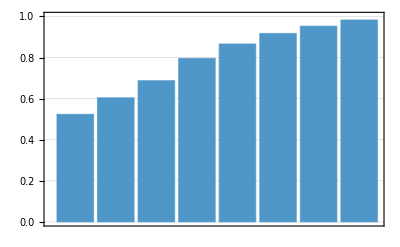

```mathematica
BarChart[{(4 π)/3,(4 π)/3+32/3 (2-√3)^3 π,5.500117935621223,6.364943546782472,6.928531487531015,7.3387098835130375,7.622029246281218,7.862276345786831}/8,PlotRange->{0,1},PlotTheme->"Detailed",ChartStyle->ColorData[97][54]]
```

```mathematica
ChartStyle->"DarkRainbow"
```

ChartStyle→DarkRainbow

```mathematica
Total[Table[i[[1]][[3]],{i,lst}]]
```

```mathematica
glist
```

```mathematica
ColorData[97,"ColorList"][[1]]
```

RGBColor[0.368417, 0.506779, 0.709798]

```mathematica
Reverse[DataPaclets`ColorData`GetBlendArgument["Rainbow"][[1;;;;3]]]
```

{RGBColor[0.878107, 0.293208, 0.160481],RGBColor[0.863512, 0.670771, 0.236564],RGBColor[0.607651, 0.743718, 0.358588],RGBColor[0.36048, 0.655759, 0.645692],RGBColor[0.24408, 0.361242, 0.816084],RGBColor[0.471412, 0.108766, 0.527016]}

```mathematica
ColorData[97][2]
```

RGBColor[0.880722, 0.611041, 0.142051]

```mathematica
colours={Red,Orange,Yellow,Green,Blue,Purple};
n=0;
llll=Table[++n;Table[{ColorData[97][n],Opacity[0.6],Sphere[{i[[1]][[1]],i[[1]][[2]],i[[1]][[3]]},i[[1]][[4]]]},{i,j}],{j,glist}];
manip=Manipulate[Show[Graphics3D[llll[[1;;f]]],PlotRange->{{0,1},{0,1},{0,1}},ViewPoint->{-3,-3,-3}],{{f,Length[llll]},Range[Length[llll]]}]
```

```mathematica
Export["cubegasket8.svg",Show[Graphics3D[llll[[1;;8]]],PlotRange->{{0,1},{0,1},{0,1}},ViewPoint->{-3,-3,-3}]]
```

cubegasket8.svg

```mathematica
llll=Table[++n;Table[Sphere[{i[[1]][[1]],i[[1]][[2]],i[[1]][[3]]},i[[1]][[4]]],{i,j}],{j,glist}];
```

```mathematica
llll
```

{{Sphere[{1,1,1},1]},{Sphere[{0.267949,0.267949,0.267949},0.267949],Sphere[{1.73205,0.267949,0.267949},0.267949],Sphere[{1.73205,1.73205,0.267949},0.267949],Sphere[{0.267949,0.267949,1.73205},0.267949],Sphere[{0.267949,1.73205,0.267949},0.267949],Sphere[{1.73205,0.267949,1.73205},0.267949],Sphere[{1.73205,1.73205,1.73205},0.267949],Sphere[{0.267949,1.73205,1.73205},0.267949]},{Sphere[{0.186702,0.186702,0.707842},0.186702],Sphere[{0.186702,0.707842,0.186702},0.186702],Sphere[{0.707842,0.186702,0.186702},0.186702],Sphere[{0.0717968,0.0717968,0.0717968},0.0717968],Sphere[{1.8133,0.186702,0.707842},0.186702],Sphere[{1.8133,0.707842,0.186702},0.186702],Sphere[{1.29216,0.186702,0.186702},0.186702],Sphere[{1.9282,0.0717968,0.0717968},0.0717968],Sphere[{1.8133,1.8133,0.707842},0.186702],Sphere[{1.8133,1.29216,0.186702},0.186702],Sphere[{1.29216,1.8133,0.186702},0.186702],Sphere[{1.9282,1.9282,0.0717968},0.0717968],Sphere[{0.186702,0.186702,1.29216},0.186702],Sphere[{0.186702,0.707842,1.8133},0.186702],Sphere[{0.707842,0.186702,1.8133},0.186702],Sphere[{0.0717968,0.0717968,1.9282},0.0717968],Sphere[{0.186702,1.8133,0.707842},0.186702],Sphere[{0.186702,1.29216,0.186702},0.186702],Sphere[{0.707842,1.8133,0.186702},0.186702],Sphere[{0.0717968,1.9282,0.0717968},0.0717968],Sphere[{1.8133,0.186702,1.29216},0.186702],Sphere[{1.8133,0.707842,1.8133},0.186702],Sphere[{1.29216,0.186702,1.8133},0.186702],Sphere[{1.9282,0.0717968,1.9282},0.0717968],Sphere[{1.8133,1.8133,1.29216},0.186702],Sphere[{1.8133,1.29216,1.8133},0.186702],Sphere[{1.29216,1.8133,1.8133},0.186702],Sphere[{1.9282,1.9282,1.9282},0.0717968],Sphere[{0.186702,1.8133,1.29216},0.186702],Sphere[{0.186702,1.29216,1.8133},0.186702],Sphere[{0.707842,1.8133,1.8133},0.186702],Sphere[{0.0717968,1.9282,1.9282},0.0717968]},{Sphere[{0.127477,0.285922,1.},0.127477],Sphere[{0.119815,0.454252,0.574067},0.119815],Sphere[{0.454252,0.119815,0.574067},0.119815],Sphere[{0.0791624,0.0791624,0.489773},0.0791624],Sphere[{0.127477,1.,0.285922},0.127477],Sphere[{0.104443,0.646179,0.459092},0.104443],Sphere[{0.454252,0.574067,0.119815},0.119815],Sphere[{0.0791624,0.489773,0.0791624},0.0791624],Sphere[{1.,0.127477,0.285922},0.127477],Sphere[{0.646179,0.104443,0.459092},0.104443],Sphere[{0.646179,0.459092,0.104443},0.104443],Sphere[{0.489773,0.0791624,0.0791624},0.0791624],Sphere[{0.0192379,0.0192379,0.0192379},0.0192379],Sphere[{0.0500267,0.0500267,0.189666},0.0500267],Sphere[{0.0500267,0.189666,0.0500267},0.0500267],Sphere[{0.189666,0.0500267,0.0500267},0.0500267],Sphere[{1.87252,0.285922,1.},0.127477],Sphere[{1.88019,0.454252,0.574067},0.119815],Sphere[{1.54575,0.119815,0.574067},0.119815],Sphere[{1.92084,0.0791624,0.489773},0.0791624],Sphere[{1.87252,1.,0.285922},0.127477],Sphere[{1.89556,0.646179,0.459092},0.104443],Sphere[{1.54575,0.574067,0.119815},0.119815],Sphere[{1.92084,0.489773,0.0791624},0.0791624],Sphere[{1.35382,0.104443,0.459092},0.104443],Sphere[{1.35382,0.459092,0.104443},0.104443],Sphere[{1.51023,0.0791624,0.0791624},0.0791624],Sphere[{1.98076,0.0192379,0.0192379},0.0192379],Sphere[{1.94997,0.0500267,0.189666},0.0500267],Sphere[{1.94997,0.189666,0.0500267},0.0500267],Sphere[{1.81033,0.0500267,0.0500267},0.0500267],Sphere[{1.87252,1.71408,1.},0.127477],Sphere[{1.88019,1.54575,0.574067},0.119815],Sphere[{1.54575,1.88019,0.574067},0.119815],Sphere[{1.92084,1.92084,0.489773},0.0791624],Sphere[{1.89556,1.35382,0.459092},0.104443],Sphere[{1.54575,1.42593,0.119815},0.119815],Sphere[{1.92084,1.51023,0.0791624},0.0791624],Sphere[{1.,1.87252,0.285922},0.127477],Sphere[{1.35382,1.89556,0.459092},0.104443],Sphere[{1.35382,1.54091,0.104443},0.104443],Sphere[{1.51023,1.92084,0.0791624},0.0791624],Sphere[{1.98076,1.98076,0.0192379},0.0192379],Sphere[{1.94997,1.94997,0.189666},0.0500267],Sphere[{1.94997,1.81033,0.0500267},0.0500267],Sphere[{1.81033,1.94997,0.0500267},0.0500267],Sphere[{0.119815,0.454252,1.42593},0.119815],Sphere[{0.454252,0.119815,1.42593},0.119815],Sphere[{0.0791624,0.0791624,1.51023},0.0791624],Sphere[{0.127477,1.,1.71408},0.127477],Sphere[{0.104443,0.646179,1.54091},0.104443],Sphere[{0.454252,0.574067,1.88019},0.119815],Sphere[{0.0791624,0.489773,1.92084},0.0791624],Sphere[{1.,0.127477,1.71408},0.127477],Sphere[{0.646179,0.104443,1.54091},0.104443],Sphere[{0.646179,0.459092,1.89556},0.104443],Sphere[{0.489773,0.0791624,1.92084},0.0791624],Sphere[{0.0192379,0.0192379,1.98076},0.0192379],Sphere[{0.0500267,0.0500267,1.81033},0.0500267],Sphere[{0.0500267,0.189666,1.94997},0.0500267],Sphere[{0.189666,0.0500267,1.94997},0.0500267],Sphere[{0.127477,1.71408,1.},0.127477],Sphere[{0.119815,1.54575,0.574067},0.119815],Sphere[{0.454252,1.88019,0.574067},0.119815],Sphere[{0.0791624,1.92084,0.489773},0.0791624],Sphere[{0.104443,1.35382,0.459092},0.104443],Sphere[{0.454252,1.42593,0.119815},0.119815],Sphere[{0.0791624,1.51023,0.0791624},0.0791624],Sphere[{0.646179,1.89556,0.459092},0.104443],Sphere[{0.646179,1.54091,0.104443},0.104443],Sphere[{0.489773,1.92084,0.0791624},0.0791624],Sphere[{0.0192379,1.98076,0.0192379},0.0192379],Sphere[{0.0500267,1.94997,0.189666},0.0500267],Sphere[{0.0500267,1.81033,0.0500267},0.0500267],Sphere[{0.189666,1.94997,0.0500267},0.0500267],Sphere[{1.88019,0.454252,1.42593},0.119815],Sphere[{1.54575,0.119815,1.42593},0.119815],Sphere[{1.92084,0.0791624,1.51023},0.0791624],Sphere[{1.87252,1.,1.71408},0.127477],Sphere[{1.89556,0.646179,1.54091},0.104443],Sphere[{1.54575,0.574067,1.88019},0.119815],Sphere[{1.92084,0.489773,1.92084},0.0791624],Sphere[{1.35382,0.104443,1.54091},0.104443],Sphere[{1.35382,0.459092,1.89556},0.104443],Sphere[{1.51023,0.0791624,1.92084},0.0791624],Sphere[{1.98076,0.0192379,1.98076},0.0192379],Sphere[{1.94997,0.0500267,1.81033},0.0500267],Sphere[{1.94997,0.189666,1.94997},0.0500267],Sphere[{1.81033,0.0500267,1.94997},0.0500267],Sphere[{1.88019,1.54575,1.42593},0.119815],Sphere[{1.54575,1.88019,1.42593},0.119815],Sphere[{1.92084,1.92084,1.51023},0.0791624],Sphere[{1.89556,1.35382,1.54091},0.104443],Sphere[{1.54575,1.42593,1.88019},0.119815],Sphere[{1.92084,1.51023,1.92084},0.0791624],Sphere[{1.,1.87252,1.71408},0.127477],Sphere[{1.35382,1.89556,1.54091},0.104443],Sphere[{1.35382,1.54091,1.89556},0.104443],Sphere[{1.51023,1.92084,1.92084},0.0791624],Sphere[{1.98076,1.98076,1.98076},0.0192379],Sphere[{1.94997,1.94997,1.81033},0.0500267],Sphere[{1.94997,1.81033,1.94997},0.0500267],Sphere[{1.81033,1.94997,1.94997},0.0500267],Sphere[{0.119815,1.54575,1.42593},0.119815],Sphere[{0.454252,1.88019,1.42593},0.119815],Sphere[{0.0791624,1.92084,1.51023},0.0791624],Sphere[{0.104443,1.35382,1.54091},0.104443],Sphere[{0.454252,1.42593,1.88019},0.119815],Sphere[{0.0791624,1.51023,1.92084},0.0791624],Sphere[{0.646179,1.89556,1.54091},0.104443],Sphere[{0.646179,1.54091,1.89556},0.104443],Sphere[{0.489773,1.92084,1.92084},0.0791624],Sphere[{0.0192379,1.98076,1.98076},0.0192379],Sphere[{0.0500267,1.94997,1.81033},0.0500267],Sphere[{0.0500267,1.81033,1.94997},0.0500267],Sphere[{0.189666,1.94997,1.94997},0.0500267]}}

```mathematica
Export["cganim.mp4",manip]
```

General::sysffmpeg: Using a limited version of FFmpeg. Install FFmpeg to get more complete codec support.

cganim.mp4

```mathematica
llll[[63]]
```

Sphere[{0.232043,0.497882,0.384149},0.105058]

```mathematica
slst =NSolve[{sphereTangencyCondition[{0.7078422344104871,0.1867023193402119,0.1867023193402119,0.1867023193402119}],y==r,z==r,(-2+√3+x)^2+(-2+√3+y)^2+(-2+√3+z)^2==(2-√3+r)^2},{x,y,z,r}];
{x,y,z,r}/.slst[[Position[r/.slst,Min[r/.slst]][[1]][[1]]]]
```

{0.489773,0.0791624,0.0791624,0.0791624}

```mathematica
lll
```

{{{2-√3,2-√3,2-√3,2-√3},{x==r,y==r,z==r,(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2}},{{0.0717968,0.0717968,0.0717968,0.0717968},{x==r,y==r,z==r,(-2+√3+x)^2+(-2+√3+y)^2+(-2+√3+z)^2==(2-√3+r)^2}},{{0.186702,0.186702,0.707842,0.186702},{x==r,y==r,(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,(-2+√3+x)^2+(-2+√3+y)^2+(-2+√3+z)^2==(2-√3+r)^2}},{{0.186702,0.707842,0.186702,0.186702},{x==r,z==r,(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,(-2+√3+x)^2+(-2+√3+y)^2+(-2+√3+z)^2==(2-√3+r)^2}},{{0.707842,0.186702,0.186702,0.186702},{y==r,z==r,(-1+x)^2+(-1+y)^2+(-1+z)^2==(1+r)^2,(-2+√3+x)^2+(-2+√3+y)^2+(-2+√3+z)^2==(2-√3+r)^2}},{{0.0192379,0.0192379,0.0192379,0.0192379},{x==r,y==r,z==r,(-0.0717968+x)^2+(-0.0717968+y)^2+(-0.0717968+z)^2==(0.0717968+r)^2}},{{0.0500267,0.0500267,0.189666,0.0500267},{x==r,y==r,(-2+√3+x)^2+(-2+√3+y)^2+(-2+√3+z)^2==(2-√3+r)^2,(-0.0717968+x)^2+(-0.0717968+y)^2+(-0.0717968+z)^2==(0.0717968+r)^2}},{{0.0500267,0.189666,0.0500267,0.0500267},{x==r,z==r,(-2+√3+x)^2+(-2+√3+y)^2+(-2+√3+z)^2==(2-√3+r)^2,(-0.0717968+x)^2+(-0.0717968+y)^2+(-0.0717968+z)^2==(0.0717968+r)^2}},{{0.189666,0.0500267,0.0500267,0.0500267},{y==r,z==r,(-2+√3+x)^2+(-2+√3+y)^2+(-2+√3+z)^2==(2-√3+r)^2,(-0.0717968+x)^2+(-0.0717968+y)^2+(-0.0717968+z)^2==(0.0717968+r)^2}}}

```mathematica
balls={1}
```

{1}

```mathematica
Join[balls,{2,3,4}]
```

{1,2,3,4}